# NNListLinePlotStack Tests

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

(last updated:  Thu 13 Feb 2014 16:48:35)

<<Set JLink` java stack size to 3072Mb>>

```mathematica
testData = 
Table[
Table[Sin[(x-n/30)*3* 2 Pi]+RandomReal[{-0.25,0.25}], {x,0,2,0.01}],
{n, 1, 10}];
```

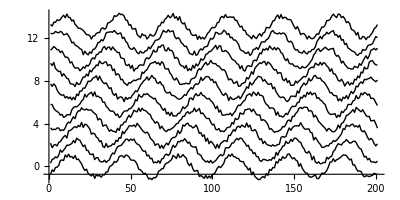

```mathematica
NNListLinePlotStack[ testData ]
```

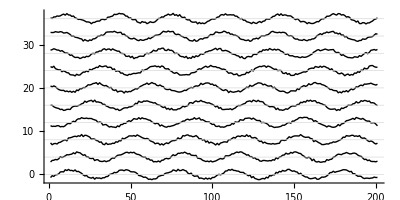

```mathematica
NNListLinePlotStack[ testData , NNStackLists-> 4,NNStackAxes->True]
```

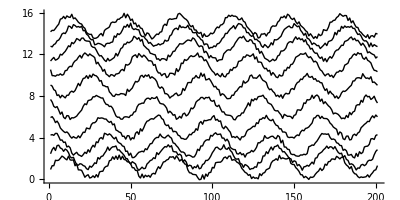

```mathematica
NNListLinePlotStack[ testData , NNStackBaselineCorrection-> 1;;5]
```